```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
ClearAll[SaveToCell]

SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

```mathematica
(*Set the front-end session option so that the currently open notebook is automatically saved whenever changes occur.*)SetOptions[$FrontEndSession,NotebookAutoSave->True]

(*Explicitly saves the current notebook.*)
NotebookSave[]

(*Clear any existing definitions for the symbol SaveToCell.This ensures we are defining it fresh here.*)
ClearAll[SaveToCell]

(*Provide usage information for the SaveToCell function.This will appear in Mathematica's documentation (via?SaveToCell) and guide users on how to use it.*)
SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand side of the assignment."

(*Set attributes for SaveToCell:-HoldFirst:This means the first argument is held unevaluated.This is important if the first argument is a symbol whose value we want to store rather than evaluate prematurely.*)
SetAttributes[SaveToCell,HoldFirst]

(*Define the SaveToCell function.Pattern:SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]] Explanation of parameters:-var_:The variable whose value will be saved.-name:An optional descriptive name for the data.By default "data".name cannot be an option (excluded by Except[_?OptionQ]).-opt:Options passed to Cell.OptionsPattern[] allows for additional Cell options to be specified.*)
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{(*Compress the current value of var into a string for storage.Compress[] takes an expression and returns a shorter,encoded string representation that can be Uncompressed later to restore the original value.*)data=Compress[var],(*Create a panel that will appear as the right-hand side of the assignment.This panel uses the provided'name' as its label and has a tooltip showing the current date and time.ToBoxes[] converts an expression into its box form suitable for display in a cell.Tooltip[] adds a tooltip (DateString[] is used for a time-stamp),and Panel[] gives a framed panel style around'name'.*)panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},(*CellPrint[] inserts a new cell into the current notebook.This new cell:-Contains code that sets var to the Uncompressed value of'data'.-The cell is formatted as an "Input" cell with certain meta-options.*)CellPrint@Cell[BoxData@RowBox[{(*MakeBoxes[var]:Converts the variable symbol to its box form*)MakeBoxes[var],"=",(*InterpretationBox is used so that the displayed content (panel) is interactive and,when evaluated,interprets to Uncompress[data],thus restoring the value of var.*)InterpretationBox[panel,Uncompress[data]],";"  (*a trailing semicolon to end the expression cleanly*)}],"Input",(*The following options are assigned to the newly created cell:*)GeneratedCell->False,(*Prevents the cell from being deleted when choosing "Delete All Output".This cell is considered user-generated rather than output.*)CellLabel->"(saved)",(*Shows a label indicating that this is a saved cell.*)opt,(*Insert any user-specified options passed into SaveToCell.*)CellLabelAutoDelete->False
(*Keeps the cell label even if the cell is edited.*)]]
```

SaveToCell[variable] creates an input cell that reassigns the current value of variable.
SaveToCell[variables, display] shows 'display' on the right-hand side of the assignment.

```mathematica
(*Description:The code below demonstrates the output generated by the SaveToCell function.Each line appears as `variable=data;` within the Mathematica notebook.However,the right-hand side is actually an InterpretationBox containing compressed data.The displayed "data" panel is just a visual representation.When you evaluate these lines,Mathematica uses Uncompress to restore the original stored values for each variable.*)

(*The name assigned to the datablocks correspond to the size of the matrices from Fig 6 and 7 of https://arxiv.org/pdf/2211.12535. The actual code is not given here as it is computationally intensive.*)
fivelisttwo="data";
fivelist="data";
fourlist="data";
threelist="data";
six12="data";
six10="data";
six8="data";
six6="data";
six4="data";
six2="data";
six0="data";
```

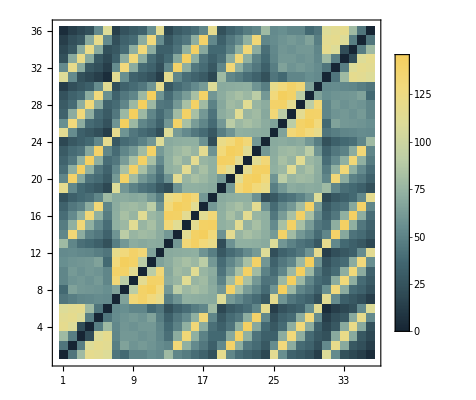

```mathematica
(*Assign a matrix variable:matrix is initially set to m612.It appears that m612 is defined elsewhere in the code.*)matrix=m612;

(*Set a threshold value.We will replace all numbers in'matrix' that are below this threshold with a fixed constant.*)
threshold=0;  (*Replace numbers below this threshold*)

(*Define the constant to replace values below the threshold.*)
fixedConstant=0;  (*Replace with this constant*)

(*Use a replacement rule on'matrix' to create'newMatrix'.For each element x in'matrix',if x<threshold,replace x with fixedConstant.The pattern x_/;x<threshold matches any element less than'threshold'.*)
newMatrix=matrix/. x_/;x<threshold:>fixedConstant;

(*Show the resulting'newMatrix' in the notebook.*)
newMatrix;

(*Parallelize[] attempts to run the enclosed computation in parallel,potentially speeding up large computations on multicore machines.*)
Parallelize[(*Compute m612:-six12 is presumably a list or array defined previously.-Partition[six12,2] partitions the list into pairs.-Count[...,{i,j}] counts how many times the pair {i,j} appears in that list.-Table[..,{i,6^2},{j,6^2}] creates a 36x36 matrix (since 6^2=36) where each entry (i,j) is the count of the pair {i,j} in the partitioned data.*)m612=Table[Count[Partition[six12,2],{i,j}],{i,6^2},{j,6^2}];
(*m612 is likely symmetric or needs to be made symmetric.Add its transpose to itself to ensure symmetry.*)m612=m612+Transpose[m612];
(*Compute m60 similarly:-Using six0,which is another data list.-Create a 36x36 matrix counting pairs {i,j} in Partition[six0,2].*)m60=Table[Count[Partition[six0,2],{i,j}],{i,6^2},{j,6^2}];
(*Make m60 symmetric by adding its transpose.*)m60=m60+Transpose[m60];
(*Now create a visual representation (ArrayPlot) of some transformation of newMatrix-m60.The Reverse[...] is likely used to flip the array visually.The commented out (#^1/(600-#)^1&/@) suggests that at one point,there was a transformation on newMatrix-m60 that has been disabled.ColorFunction->"StarryNightColors" applies a predefined color gradient.Frame->True shows a frame around the plot.FrameTicks->{...} sets up custom ticks.In this case,it uses a variable d=6 and creates ticks for a 36x36 grid.FrameLabel->{{None,None},{None,None}} means no frame labels on the axes.FrameTicksStyle changes the style of the ticks.ColorFunctionScaling->True means the color function automatically scales the data values.PlotLegends->Automatic includes a color legend for the plot.TicksStyle->Directive[Thick] makes the ticks thicker.*)new=ArrayPlot[Reverse[newMatrix-m60],ColorFunction->"StarryNightColors",Frame->True,FrameTicks->{d=6;
Table[{i,d^2-i+1},{i,Range[d^2]}],Range[d^2]},FrameLabel->{{None,None},{None,None}},FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontWeight->Bold,12],ColorFunctionScaling->True,PlotLegends->Automatic,TicksStyle->Directive[Thick]]] (*End of Parallelize block*)
```

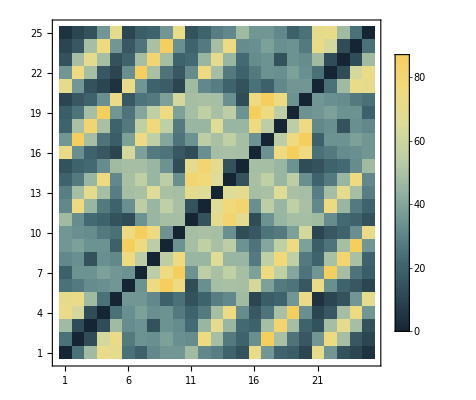

```mathematica
matrix=m514;
threshold=0;  (*Replace numbers below this threshold*)
fixedConstant=0;  (*Replace with this constant*)
newMatrix=matrix/. x_/;x<threshold:>fixedConstant;
newMatrix;
Parallelize[m514=Table[Count[Partition[fivelisttwo[[2]],2],{i,j}],{i,5^2},{j,5^2}];m514=m514+Transpose[m514];
m50=Table[Count[Partition[fivelist[[1]],2],{i,j}],{i,5^2},{j,5^2}];m50=m50+Transpose[m50];
ArrayPlot[Reverse[(*#^1/(300-#)^1&/@*)newMatrix-m50],ColorFunction->"StarryNightColors",Frame->True,FrameTicks->{d=5;Table[{i,d^2-i+1},{i,Range[d^2]}],Range[d^2]},FrameLabel->{{None,None},{None,None}},FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontWeight->Bold, 8],ColorFunctionScaling->True,PlotLegends->Automatic,TicksStyle->Directive[Thick]]]
```

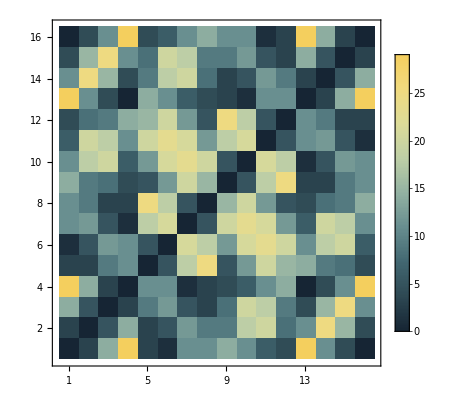

```mathematica
matrix=m410;
threshold=0;  (*Replace numbers below this threshold*)
fixedConstant=0;  (*Replace with this constant*)
newMatrix=matrix/. x_/;x<threshold:>fixedConstant;
newMatrix;
m410=Table[Count[Partition[fourlist[[11]],2],{i,j}],{i,4^2},{j,4^2}];m410=m410+Transpose[m410];
m40=Table[Count[Partition[fourlist[[1]],2],{i,j}],{i,4^2},{j,4^2}];m40=m40+Transpose[m40];
ArrayPlot[Reverse[(*#^1/(90-#)^0&/@*)newMatrix-m40],ColorFunction->"StarryNightColors",Frame->True,FrameTicks->{d=4;Table[{i,d^2-i+1},{i,Range[d^2]}],Range[d^2]},FrameLabel->{{None,None},{None,None}},FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontWeight->Bold, 10],ColorFunctionScaling->True,PlotLegends->Automatic,TicksStyle->Directive[Thick]]
```

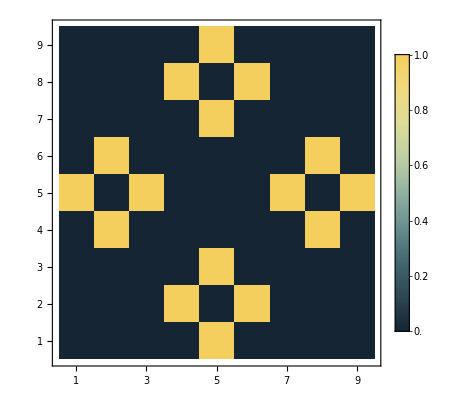

```mathematica
matrix=m310;
threshold=0;  (*Replace numbers below this threshold*)
fixedConstant=0;  (*Replace with this constant*)
newMatrix=matrix/. x_/;x<threshold:>fixedConstant;
newMatrix;
m310=Table[Count[Partition[threelist[[11]],2],{i,j}],{i,3^2},{j,3^2}];m310=m310+Transpose[m310];
m30=Table[Count[Partition[threelist[[1]],2],{i,j}],{i,3^2},{j,3^2}];m30=m30+Transpose[m30];
ArrayPlot[Reverse[newMatrix-m30],ColorFunction->"StarryNightColors"(*,ColorRules->{1->Yellow,0->Black}*),Frame->True,FrameTicks->{d=3;Table[{i,d^2-i+1},{i,Range[d^2]}],Range[d^2]},FrameLabel->{{None,None},{None,None}},TicksStyle->Directive[Thick],FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontWeight->Bold, 12],ColorFunctionScaling->True,PlotLegends->Automatic,PlotLegends->{Automatic,Style[FontFamily->"Times New Roman",FontWeight->Bold, 12]}]
```

```mathematica
(*The following lines define several lists (lXX) that count how many times each integer from 1 to n^2 appears in a given list.Here "six0","six2","six4",etc.appear to be previously defined lists (or data sets).Each line uses Table and Count:-Table creates a list by iterating i from 1 to n^2.-Count[list,i] counts how many times the value i appears in'list'.*)(*For the 6x6 datasets (6^2=36):*)l60=Table[Count[six0,i],{i,6^2}];
l62=Table[Count[six2,i],{i,6^2}];
l64=Table[Count[six4,i],{i,6^2}];
l66=Table[Count[six6,i],{i,6^2}];
l68=Table[Count[six8,i],{i,6^2}];
l610=Table[Count[six10,i],{i,6^2}];
l612=Table[Count[six12,i],{i,6^2}];

(*For the 5x5 datasets (5^2=25):"fivelist" and "fivelisttwo" appear to be lists of lists,so indexing like fivelist[[1]] retrieves the first sublist,fivelist[[2]] the second,etc.Each Count operation is counting occurrences of i in a particular sublist.*)
l50=Table[Count[fivelist[[1]],i],{i,5^2}];
l52=Table[Count[fivelist[[2]],i],{i,5^2}];
l54=Table[Count[fivelist[[3]],i],{i,5^2}];
l56=Table[Count[fivelist[[4]],i],{i,5^2}];
l58=Table[Count[fivelist[[5]],i],{i,5^2}];
l510=Table[Count[fivelist[[6]],i],{i,5^2}];
l512=Table[Count[fivelisttwo[[1]],i],{i,5^2}];
l514=Table[Count[fivelisttwo[[2]],i],{i,5^2}];

(*For the 4x4 datasets (4^2=16):Similarly,"fourlist" is likely a list of multiple sublists at odd indices.*)
l40=Table[Count[fourlist[[1]],i],{i,4^2}];
l42=Table[Count[fourlist[[3]],i],{i,4^2}];
l44=Table[Count[fourlist[[5]],i],{i,4^2}];
l46=Table[Count[fourlist[[7]],i],{i,4^2}];
l48=Table[Count[fourlist[[9]],i],{i,4^2}];
l410=Table[Count[fourlist[[11]],i],{i,4^2}];

(*For the 3x3 datasets (3^2=9):Similarly,"threelist" is a list where data is taken from every second sublist (odd indices).*)
l30=Table[Count[threelist[[1]],i],{i,3^2}];
l32=Table[Count[threelist[[3]],i],{i,3^2}];
l34=Table[Count[threelist[[5]],i],{i,3^2}];
l36=Table[Count[threelist[[7]],i],{i,3^2}];
l38=Table[Count[threelist[[9]],i],{i,3^2}];
l310=Table[Count[threelist[[11]],i],{i,3^2}];

(*In summary:Each lXX variable holds a frequency distribution of integers within a given dataset.The indexing patterns (like fivelist[[1]],fivelist[[2]],etc.) suggest that these lists contain multiple subsets or trials,and you're extracting the frequency counts of integers in each subset.The pattern suggests a data structure where "fivelist","fourlist",and "threelist" each contain multiple sublists.You are counting occurrences of each integer i in those sublists to build frequency arrays for further analysis or plotting.*)
```

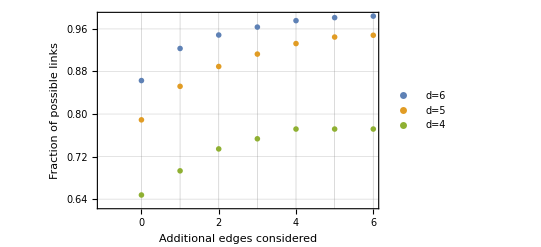

```mathematica
ListPlot[{{(*For d=6:Each element calculates the mean of l6X arrays,divides by 19635,and uses N[] to ensure a numerical approximation.Mean[l60]/19635 is the average frequency for the "l60" dataset normalized by 19635 (likely a total count or possible link count).*)N[Mean[l60]/19635],N[Mean[l62]/19635],N[Mean[l64]/19635],N[Mean[l66]/19635],N[Mean[l68]/19635],N[Mean[l610]/19635],N[Mean[l612]/19635]},{(*For d=5:Similar calculations for the "l5X" arrays,normalized by 6072.*)N[Mean[l50]/6072],N[Mean[l52]/6072],N[Mean[l54]/6072],N[Mean[l56]/6072],N[Mean[l58]/6072],N[Mean[l510]/6072],N[Mean[l512]/6072]},{(*For d=4:Similar calculations for the "l4X" arrays,normalized by 1365. Note:l410 appears twice,which might be intentional or a placeholder.*)N[Mean[l40]/1365],N[Mean[l42]/1365],N[Mean[l44]/1365],N[Mean[l46]/1365],N[Mean[l48]/1365],N[Mean[l410]/1365],N[Mean[l410]/1365]}
(*A fourth series for d=3 is commented out.If uncommented,it would similarly compute normalized means for the l3X arrays.*)
(*,{N[Mean[l30]/168],N[Mean[l32]/168],N[Mean[l34]/168],N[Mean[l36]/168],N[Mean[l38]/168],N[Mean[l310]/168]}*)},(*Add plot legends to distinguish each set of data.They correspond to "d=6","d=5",and "d=4" sets.*)PlotLegends->(Style[#,FontFamily->"Times New Roman",FontWeight->Bold,12]&/@{"d=6","d=5","d=4"}),(*Use a frame around the plot rather than standard axes.*)Frame->True,(*Customize the frame ticks:-On the vertical axes:All default ticks appear.-On the horizontal axis:Explicitly list ticks with {1,0},{2,1},etc.This likely re-labels the x-axis values to a shifted scale.The second set of ticks (None) indicates no top axis ticks.*)FrameTicks->{{All,All},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5},{7,6}},None}},(*Style the ticks with a specified font and weight.*)FrameTicksStyle->Directive[FontFamily->"Times New Roman",FontWeight->Bold,12],(*Make tick marks thicker for better visibility.*)TicksStyle->Directive[Thick],(*Use open markers for each data point on the plot.*)PlotMarkers->"OpenMarkers",(*Add labels to the frame axes:-Left y-axis:"Fraction of possible links"-Bottom x-axis:"Additional edges considered" No labels on top and right axes.*)FrameLabel->{{"Fraction of possible links",None},{"Additional edges considered ",None}},(*Style the labels with a specific font,weight,and size.*)LabelStyle->Directive[FontFamily->"Times New Roman",FontWeight->Bold,12],(*Add automatic grid lines to help read the values.*)GridLines->Automatic]
```